# 7

## PHAS2443: Practical Mathematics II Lecture 7: Modelling with Particles

Many of the properties of materials can be described by modelling the particles which make up the material as though they were classical particles subject to Newton's laws of motion. This applies to solids, liquids and gases, where the particles are atoms or molecules interacting through intermolecular potentials (of course, the detailed forms of those potentials depend on quantum mechanics); to solutions and plasmas, where positive and negative ions, or ions and electrons, interact through a mixture of short-range intermolecular potentials and long-range Coulomb potentials; and to astrophysical systems interacting through gravity. In addition, particles may be used to model 'chunks' of matter, especially in fluid flow simulations.

## Systems of particles: from molecules to galaxies.

When we deal with atoms and molecules, as opposed to ions, the interactions between them typically interact through the Lennard-Jones potential, which is often written in the form
 V(r) = 4 ϵ [(σ/r)^12 - (σ/r)^6],
 where ϵ represents the strength of the interaction, and σ is a measure of the atomic radius and is characterised by V(σ)=0. Defining the minimum distance r_m as r_m=2^(1/6)σ≈1.12σ, the Lennard-Jones potential can be rewritten 
 V(r) = ϵ [(r_m/r)^12-2(r_m/r)^6],
and V(r_m)=-ϵ. 
 The interaction resembles the following diagram:

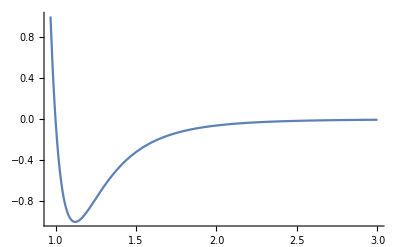

```mathematica
Plot[Evaluate[4 ϵ ((σ/r)^12-(σ/r)^6)/.ϵ->1/.σ->1],{r,0.0001,3},PlotRange->{All,{-1,1}}]
```

Note the sharp rise at small separations (not very different from a 'hard-sphere' contact), and the attractive interaction for medium to large separations. Obviously, given this potential we can calculate the force on any molecule due to the presence of any other molecule, add all the forces, and thus find the acceleration. Then we can integrate the equations (probably using a scheme such as the Verlet scheme described in the exercises that accompanied Lecture 4).  

This is known as the molecular dynamics method. We can use the results to predict the properties of the material.  

"What properties?" you may ask. The molecular dynamics method is surprisingly effective: it can produce equations of state for gases, predict changes of state such as vapourisation and melting, model the way in which defects in materials clump together, show how materials break under strain, and so on.  Unfortunately, some of these calculations require millions of atoms to be simulated, and we shall have to be much less ambitious.
    
    First, let us set up a simple scheme for calculations for neon (Ne) atoms. The interactions can be described by a Lennard-Jones potential with σ=0.275 nm and ϵ=36 k_B where k_B is the Boltzmann's constant, showing that the binding energy is characterised by a temperature of 36 K.

params={σ→ 0.275 10^-9,ϵ→36 1.38 10^-23,m→20.2  1.673 10^-27} ;
v[r_]:=4 ϵ ((σ/r)^12 - (σ/r)^6)
dv[r_]=D[v[r],r];
acc[rrel_List]:=If[rrel=={0.,0.,0.},
                                                0,
                                                4 ϵ ((6 σ^6)/(rrel.rrel)^4-(12 σ^12)/(rrel.rrel)^7)rrel]/m/.params

The only subtlety in this is the recognition that force and acceleration are vectors, so that if r_12 is the vector from atom 1 to atom 2, i.e. r_2-r_1, then the force will be along the line of centres, in the direction (r̂)_12 = r_12/|r_12|. This explains why we differentiate ((r̂)_12)/r_12^6 with respect to r_12 to get (-6(r̂)_12)/r_12^7 = (-6 r_12)/r_12^8=(-6 r_12)/(r_12.r_12)^4, and similarly for ((r̂)_12)/r_12^12, i.e. (-6 r_12)/(r_12.r_12)^7.

Now set up a three dimensional box, with sides L, and place n atoms at random in this box. Our data structure will keep, for each atom, its current and last positions. We set up the data so that the current and last positions are the same, that is, initially the atoms are at rest. Our data structure is going to be in the form
  {{{current x for particle 1,current y for particle 1, current z for particle 1},
    {previous x for particle 1,previous y for particle 1, previous z for particle 1}},
   {{current x for particle 2,current y for particle 2, current z for particle 1},
    {previous x for particle 2,previous y for particle 2, previous z for particle 2}},
   ...}.

init[n_,L_]:=dat=Table[L RandomReal[{0,1},3],{i,1,n}]/.{x_,y_,z_}→{{x,y,z},{x,y,z}}/.params
accvec[dat_]:=Map[Apply[Plus,#]&,Outer[acc[#1[[1]]-#2[[1]]]&,dat,dat,1]]

#### Explanation:

```mathematica
Table[L RandomReal[{0,1},3],{i,1,n}]
```

sets up the list of n triples of {x,y,z} each in the range 0 to L

```mathematica
/.{x_,y_,z_}->{{x,y,z},{x,y,z}}
```

duplicates each triple (as these will then be used as the positions at the first two time steps it corresponds to starting from rest)

```mathematica
/.params
```

substitutes in the numerical values of the parameters.

```mathematica
Outer[acc[#1[[1]]-#2[[1]]]&,dat,dat,1]
```

takes all the possible pairings of the current positions (current because of the [[1]] attached to each #) of the particles (the final 1 ensures that we only pair {x,y,z} with {x',y',z'}, and not all the possible combinations of x with x', x with y', and so on). The difference vector is passed to the acceleration-calculating routine acc, so the result of this is a two-dimensional table giving the acceleration of particle i as a result of its interaction with particle j.

```mathematica
accvec[dat_]:=Map[Apply[Plus,#]&,...]
```

By Mapping Apply Plus onto the two-dimensional table, we go inside the outer list brackets, and replace the head of each inner list with Plus: that is, we add the contributions of all the particles to the acceleration of every particle, resulting in a vector {{x acceleration 1, y acceleration 1, z acceleration 1},...}.

For instance let us consider a list of  two particles and apply the accvec function by step

par={{{x1,y1,z1},{x1’,y1’,z1’}},{{x2,y2,z2},{x2’,y2’,z2’}}};
       Outer[#1[[1]]-#2[[1]]&,par,par,1]
       Map[Apply[Plus,#]&,Outer[#1[[1]]-#2[[1]]&,par,par,1]]

We will get the two following outputs

{{{0,0,0},{x1-x2,y1-y2,z1-z2}},{{-x1+x2,-y1+y2,-z1+z2},{0,0,0}}}
{{x1-x2,y1-y2,z1-z2},{-x1+x2,-y1+y2,-z1+z2}}

We shall integrate the equations with the simple Störmer–Verlet scheme:
         x(t+Δt)=2x(t)-x(t-Δt)+Δt^2(F(x(t)))/m,
with the velocity, if we need it, at time t calculated as
         v(t)=(x(t+Δt) - x(t-Δt))/(2 Δt)

upd[d_,Δt_]:=Module[{a,tt},
tt=Transpose[d];
a=accvec[d];
Transpose[{2 tt[[1]]-tt[[2]]+Δt^2 a,tt[[1]]}]
      ]

#### Explanation

```mathematica
tt=Transpose[d];
```

creates a new list from {{{x1now,y1now,z1now},{x1last,y1last,z1last}},{{x2now, ...},{}},...} i.e. {{r1now,r1last},{r2now,...},...}, so that tt is {{r1now,r2now,...},{r1last,...},...}.

```mathematica
a=accvec[d];
```

forms the acceleration vector {a1,a2,...}

```mathematica
Transpose[{2 tt[[1]]-tt[[2]]+Δt^2 a,tt[[1]]}]
```

then updates, each rn becoming rnnext = 2 rnnow-rnlast+Δt^2an, forms the list {{r1next,r2next...}, {r1now...}}, and Transposes it back to form {{r1next,r1now},{r2next,r2now}...}.

Now do a calculation and display the results.

SeedRandom[2010]; (*initialise seed's random number generator*) 
blen=10^-9;
init[5,blen];
fin=Nest[upd[#,10^-14]&,dat,100];
pp[atoms_,L_]:=Show[Graphics3D[{Red,Line[{{0,0,0},{0,0,L},{0,L,L},{0,L,0},{0,0,0},{L,0,0},{L,0,L},{L,L,L},{L,L,0},{L,0,0}}],Line[{{0,0,L},{L,0,L}}],Line[{{0,L,L},{L,L,L}}],Line[{{0,L,0},{L,L,0}}],Blue,PointSize[0.05],Map[Point,Transpose[atoms][[1]]]}],Boxed→True,PlotRange→{{0,L},{0,L},{0,L}}]
pp[fin,blen]

-Graphics3D-

#### Explanation:

```mathematica
blen=10^-9;
```

sets the length of the side of the computational box

```mathematica
init[5,blen];
```

initiates 5 atoms at rest in the box

```mathematica
fin=Nest[upd[#,10^-14]&,dat,100];
```

and loops the update function 100 times with a suitably short time step. Note that for Nest to work the output from upd has to be identical in structure to the input.

Now we define a function which will draw the box and the particles.

```mathematica
pp[atoms_,L_]:=Show[Graphics3D[{Line[{{0,0,0},{0,0,L},{0,L,L},{0,L,0},{0,0,0},{L,0,0},{L,0,L},{L,L,L},{L,L,0},{L,0,0}}],Line[{{0,0,L},{L,0,L}}],Line[{{0,L,L},{L,L,L}}],Line[{{0,L,0},{L,L,0}}],PointSize[0.05],Map[Point,Transpose[atoms][[1]]]}],Boxed->True,PlotRange->{{0,L},{0,L},{0,L}}]
```

The argument of Graphics3D is a list of graphics primitives:

```mathematica
Line[{{0,0,0},{0,0,L},{0,L,L},{0,L,0},{0,0,0},{L,0,0},{L,0,L},{L,L,L},{L,L,0},{L,0,0}}],Line[{{0,0,L},{L,0,L}}],Line[{{0,L,L},{L,L,L}}],Line[{{0,L,0},{L,L,0}}]
```

is a set of lines to draw the box, and

```mathematica
PointSize[0.05],Map[Point,Transpose[atoms][[1]]]
```

increases the point size to make the atoms more visible and Maps Point onto the current positions of the atoms (the reason for Transpose is given above).

```mathematica
pp[fin,blen]
```

plots the final positions.

We can see a problem -- our atoms are 'escaping' (if you don't see this, run the code again with a different seed to the function SeedRandom[] -- that will provide different starting conditions thus different results). There are two ways of fixing this. One is to imagine that the box has rigid walls, so that whenever a particle encounters the wall it bounces elastically off it. The other is to imagine that our box represents a small volume of a material (gas, liquid or solid), each of which is behaving in the same way, so that if a particle leaves through, say, the top of our box it will be replaced by the particle leaving the top of the box below and entering the bottom of our box. This gives 'periodic boundary conditions', and this is the scheme we shall adopt.

In order to do this, we have to do two things:
   1. In calculating potentials, we have to add the interactions with 'image' particles in neighbouring boxes. We don't, however, want to include the interaction of a particle with its own image. The easiest way to ensure the last condition is to force the potential to go to zero at a distance a little less than the length of a side of the box. We can do this crudely:

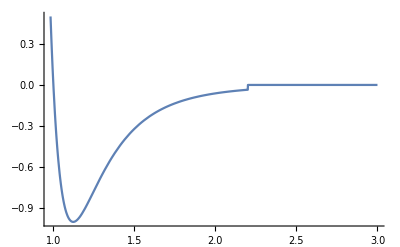

```mathematica
Plot[Evaluate[If[r<2.2,4 ϵ ((σ/r)^12-(σ/r)^6)/.ϵ->1/.σ->1,0]],{r,0.0001,3},PlotRange->{All,{-1,0.5}}]
```

The problem with this is that there is a discontinuity in the potential at the cut-off distance, which means that there will be a small but sudden change as two particles approach each other and the interaction 'switches on'. This might lead to numerical problems, and it is generally better to take the potential smoothly to zero.

 2. If a time step takes a particle through a boundary of the box, we must ensure that it reappears on the other side. There is a slight problem then, as if we try to evaluate the velocity it will look as if it is large, and in the wrong direction. This is shown in the diagram below: green represents the previous position and red the current, and we need to transform from

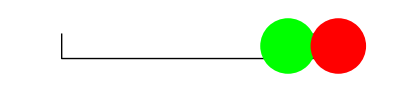

```mathematica
Show[Graphics[{Line[{{-5,1},{-5,0},{5,0},{5,1}}],PointSize[0.1],RGBColor[0,1,0],Point[{4.,0.5}],Arrow[{{4.5,0.5},{5.,0.5}}],RGBColor[1,0,0],Point[{6.,0.5}],Arrow[{{6.5,0.5},{7.,0.5}}]}],AspectRatio->Automatic,PlotRange->{{-6,7},{-1,2}}]
```

to

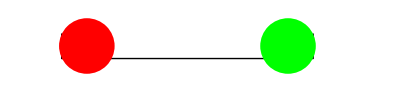

```mathematica
Show[Graphics[{Line[{{-5,1},{-5,0},{5,0},{5,1}}],PointSize[0.1],RGBColor[0,1,0],Point[{4.,0.5}],Arrow[{{4.5,0.5},{5.,0.5}}],RGBColor[1,0,0],Point[{-4.,0.5}],Arrow[{{-3.5,0.5},{-3.,0.5}}]}],AspectRatio->Automatic,PlotRange->{{-6,7},{-1,2}}]
```

We can achieve the periodicity by always working out positions modulo L: for example

```mathematica
Mod[0.9,1.0]
Mod[1.1,1.0]
Mod[-0.1,1.0]
```

0.9

0.1

0.9

We will do the same with the interactions. We shall ignore interactions involving particles more than half the cell side apart, but we shall consider interactions of particles with image particles in neighbouring cells. This leads, for example, to the following. Here we show as solid circles real positions of atoms, their images as outlines, and we draw lines to show which interactions are used.

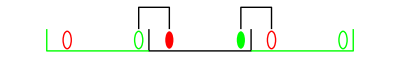

```mathematica
Show[Graphics[{Line[{{-5,1},{-5,0},{5,0},{5,1}}],Line[{{-3,1},{-3,2},{-6,2},{-6,1}}],Line[{{4,1},{4,2},{7,2},{7,1}}],RGBColor[0,1,0],Line[{{-15,1},{-15,0},{-5,0}}],Line[{{5,0},{15,0},{15,1}}],Disk[{4.,0.5},0.4],Circle[{14.,0.5},0.4],Circle[{-6.,0.5},0.4],RGBColor[1,0,0],Disk[{-3.,0.5},0.4],Circle[{7.,0.5},0.4],Circle[{-13.,0.5},0.4]}],AspectRatio->Automatic,PlotRange->{{-16,16},{-1,2}}]
```

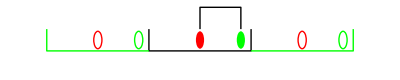

```mathematica
Show[Graphics[{Line[{{-5,1},{-5,0},{5,0},{5,1}}],Line[{{0,1},{0,2},{4,2},{4,1}}],RGBColor[0,1,0],Line[{{-15,1},{-15,0},{-5,0}}],Line[{{5,0},{15,0},{15,1}}],Disk[{4.,0.5},0.4],Circle[{14.,0.5},0.4],Circle[{-6.,0.5},0.4],RGBColor[1,0,0],Disk[{0.,0.5},0.4],Circle[{10.,0.5},0.4],Circle[{-10.,0.5},0.4]}],AspectRatio->Automatic,PlotRange->{{-16,16},{-1,2}}]
```

It is probably easier to work with the velocity Verlet algorithm, as then we only need to alter the current position when a box boundary is crossed -- the velocity is not changed. In this scheme
           x(t+Δ t) = x(t) + Δ t  v(t) +(Δ t)^2 (F(x(t)))/(2m),
          v(t+Δ t) = v(t) + Δ t (F(x(t+Δ t))+F(x(t)))/(2m).
  We can implement the potential including the interaction with

accper[rrel_List,L_]:=If[rrel=={0.,0.,0.},0,rr=Map[Which[#>L/2,#-L,#<-L/2,#+L,True,#]&,rrel];4 ϵ ((6 σ^6)/(rr.rr)^4-(12 σ^12)/(rr.rr)^7)rr]/m/.params

#### Explanation:

Our new acceleration function for periodic boundary conditions is

```mathematica
accper[rrel_List,L_]:=If[rrel=={0.,0.,0.},0,
```

and after checking that we are not looking at a self-interaction we form a new vector between the atoms, rr.

```mathematica
rr=Map[Which[#>L/2,#-L,#<-L/2,#+L,True,#]&,rrel];
```

Remember that rrel is a list of length 3, representing {x,y,z}, so by Mapping this Which function onto it we can check whether we are looking at this (periodic) interaction between atoms more than half a box-length apart, and if so take the interaction with the (nearer) image in the neighbouring cell. We then evaluate the acceleration vector with this, possibly modified, separation vector rr.

```mathematica
4 ϵ ((6 σ^6)/(rr.rr)^4-(12 σ^12)/(rr.rr)^7)rr]/m/.params
```

As we are using the velocity Verlet algorithm our data structure now contains the positions and the velocities of the particles. Actually, we'll now be a bit more careful about setting up the positions, and avoid close contacts. One way of doing this is to look at the total energy of the system

potenper[rrel_List,L_]:=If[rrel=={0.,0.,0.},0,rr=Map[Which[#>L/2,#-L,#<-L/2,#+L,True,#]&,rrel];4 ϵ (σ^12/(rr.rr)^6-σ^6/(rr.rr)^3)]/.params
etot[dat_,L_]:=Plus@@Flatten[Outer[potenper[#1-#2,L]&,dat,dat,1]]/2

#### Explanation

```mathematica
If[rrel=={0.,0.,0.},0,rr=Map[Which[#>L/2,#-L,#<-L/2,#+L,True,#]&,rrel];4 ϵ (σ^12/(rr.rr)^6-σ^6/(rr.rr)^3)]/.params
```

Here the implementation of the periodicity is just the same as in accper above, and the only difference is that we are evaluating the potential energy. For the vector separation rrel, potenper returns the potential energy corresponding to that separation.

```mathematica
etot[dat_,L_]:=Plus@@Flatten[Outer[potenper[#1-#2,L]&,dat,dat,1]]/2
```

Again, the use of Outer is similar to that in the calculation of the accelerations. However, as we want the total energy we want to sum all the pairwise interactions: that is why we Flatten first, to convert what Outer returns, which is in the form {{0,pot12,pot13,...},{pot21,0,pot23...},...}, to the form {0, pot12, pot13, ..., pot21, 0, pot23, ...}. Applying Plus to this (Plus@@f is the same as Apply[Plus,f]) gives us double the total energy, as by including pot12 as well as pot21 it counts each interaction twice -- hence the division by 2.

and keep initialising until we get a small enough total energy (actually what is often done is to arrange the atoms on a regular lattice, as if they were atoms in a crystal, and then move them slightly away form the ideal positions)

initper[n_,L_]:=For[en=10^10;tries=0,(Abs[en]>ϵ/.params)&&(tries<100),tries++,dat=Table[{L RandomReal[{0,1},3],{0.,0.,0.}},{i,1,n}]/.params;en=etot[Transpose[dat][[1]],L]]

#### Explanation

The initialisation routine uses a For loop, making up to 100 attempts to find a suitable starting configuration. Remember that the usage of a For command is For[startup commands, termination condition, update loop variable, actions]

```mathematica
initper[n_,L_]:=For[en=10^10;tries=0,
```

We start with a huge energy, so that the termination condition has an initial value to check

```mathematica
(Abs[en]>ϵ/.params)&&(tries<100),
```

stop the loop if the energy is low enough or if we have had 100 attempts,

```mathematica
tries++,
```

this is just a shorthand for updating the counter, and is equivalent to tries=tries+1,

```mathematica
dat=Table[{L RandomReal[{0,1},3],{0.,0.,0.}},{i,1,n}]/.params;
```

set up a table of random positions in the box (the second element of the two-element list is not any longer the previous position but the velocity and we set it initially to zero). The list we pass to etot has the right form.

```mathematica
en=etot[Transpose[dat][[1]],L]]
```

we need a new scheme for the acceleration vector, which is just the same as the one we had before except that it uses accper instead of acc:

accvecper[dat_,L_]:=Map[Apply[Plus,#]&,Outer[accper[#1-#2,L]&,dat,dat,1]]

Alter the plotting so as to include the velocities

ppper[atoms_,L_]:=Module[{x,v,vsc},{x,v}=Transpose[atoms];vsc=Max[Abs[v]];vsc=If[vsc==0,0,0.2 L/vsc];Show[Graphics3D[{Line[{{0,0,0},{0,0,L},{0,L,L},{0,L,0},{0,0,0},{L,0,0},{L,0,L},{L,L,L},{L,L,0},{L,0,0}}],Line[{{0,0,L},{L,0,L}}],Line[{{0,L,L},{L,L,L}}],Line[{{0,L,0},{L,L,0}}],PointSize[0.05],Map[Point,x],Map[Line[{#[[1]],#[[1]]+#[[2]]vsc}]&,atoms]}],Boxed→True,PlotRange→{{0,L},{0,L},{0,L}}]]

#### Explanation

This plotting routine is very similar to the previous one: we start by setting up separate lists of positions and velocities.

```mathematica
ppper[atoms_,L_]:=Module[{x,v,vsc},{x,v}=Transpose[atoms];
```

Set up a scaling for the velocity, so that the greatest velocity vector corresponds to 0.2 of the side of the box:

```mathematica
vsc=Max[Abs[v]];vsc=If[vsc==0,0,0.2 L/vsc];
```

Most of the graphical output is the same as before,

```mathematica
Show[Graphics3D[{Line[{{0,0,0},{0,0,L},{0,L,L},{0,L,0},{0,0,0},{L,0,0},{L,0,L},{L,L,L},{L,L,0},{L,0,0}}],Line[{{0,0,L},{L,0,L}}],Line[{{0,L,L},{L,L,L}}],Line[{{0,L,0},{L,L,0}}],PointSize[0.05],Map[Point,x],Map[Line[{#[[1]],#[[1]]+#[[2]]vsc}]&,atoms]}],Boxed->True,PlotRange->{{0,L},{0,L},{0,L}}]]
```

but we have inserted

```mathematica
Map[Line[{#[[1]],#[[1]]+#[[2]]vsc}]&,atoms]
```

to produce lines from the current positions of the atoms (#[[1]]) in the direction of the velocity, appropriately scaled.

and the update scheme is as follows (this is not very efficient, but it shows the relationship with the original expressions fairly clearly). A more practical scheme would include a variable time-step, so that shorter steps would be taken when accelerations are large.

updvVper[d_,Δt_,L_]:=Module[{a,an,x,xn,v},
{x,v}=Transpose[d];
a=accvecper[x,L];
xn=Mod[x +Δt v+Δt^2 a/2,L];
an=accvecper[xn,L];
Transpose[{xn,v+Δt(a+an)/2 }]]

#### Explanation:

```mathematica
updvVper[d_,Δt_,L_]:=Module[{a,an,x,xn,v},
```

sets up a, an, x, xn and v as local variables,

```mathematica
{x,v}=Transpose[d];
```

separates x and v out of the input list d (probably inefficient, but it makes it easier to follow the rest),

```mathematica
a=accvecper[x,L];
```

calculates the acceleration vector based on the current position,

```mathematica
xn=Mod[x +Δt v+Δt^2 a/2,L];
```

estimates the new position,

```mathematica
an=accvecper[xn,L];
```

calculates the updated acceleration, an,

```mathematica
Transpose[{xn,v+Δt(a+an)/2 }]
```

and finally updates the velocity using the average of the original and updated accelerations.

Now let's set up and run again: this is just what we did before, but with the functions modified for the periodic case.

blen=10^-8;
initper[10,blen];
tries
en
fin=dat;
ListAnimate[Table[fin=Nest[updvVper[#1,10^-11,blen]&,fin,10];ppper[fin,blen],{i,1,100}]]

1

-1.49196×10^-25

Plot a histogram of the particle speeds.

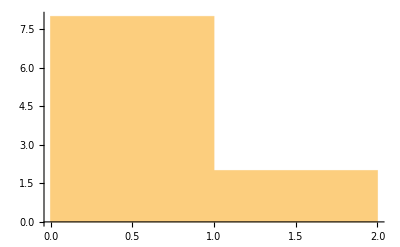

```mathematica
Histogram[(√(#1.#1)&)/@Transpose[fin]⟦2⟧]
```

If we run the same calculation with more atoms, we find (this will take quite a while to execute)

```mathematica
blen=10^-8;
initper[50,blen]
tries
en
fin=dat;
Timing[fin=Nest[updvVper[#1,10^-11,blen]&,fin,100];]
```

4

-2.89164×10^-23

{104.454,Null}

```mathematica
fin
```

{{{2.705×10^-10,7.58828×10^-9,8.32782×10^-9},{-4.25746,-1.94384,1.37487}},{{2.86834×10^-9,8.37597×10^-10,4.59811×10^-9},{-0.838663,1.25328,1.45786}},{{7.50555×10^-9,4.10508×10^-9,5.17424×10^-9},{-1.47931,-2.0346,-2.0938}},{{2.13873×10^-9,1.95526×10^-9,8.35548×10^-9},{0.339622,-0.829404,-1.14307}},{{5.24484×10^-9,1.91054×10^-10,9.64288×10^-9},{-4.90017,-2.58712,8.76503}},{{1.31391×10^-11,6.86423×10^-9,6.83995×10^-9},{-6.39668,3.58988,-2.29111}},{{7.67678×10^-9,2.60271×10^-9,8.78218×10^-9},{12.8088,0.444103,7.97784}},{{3.62896×10^-9,5.45533×10^-9,2.27452×10^-9},{1.53022,-1.83322,1.04606}},{{8.30357×10^-9,5.19012×10^-9,5.87146×10^-9},{-0.565902,-0.0837317,-0.969493}},{{9.61234×10^-9,1.85024×10^-9,9.4444×10^-9},{-0.267286,2.31964,-1.78363}},{{2.35666×10^-10,3.84139×10^-9,8.41364×10^-9},{12.8856,-0.20277,1.55684}},{{5.66955×10^-9,6.37729×10^-9,1.19849×10^-9},{1.57744,-1.93361,0.627465}},{{5.20445×10^-9,1.19384×10^-9,7.37177×10^-9},{0.318329,-0.40316,-0.761992}},{{6.65107×10^-9,2.24108×10^-9,7.88494×10^-10},{8.86917,3.78884,-2.96346}},{{6.94148×10^-9,5.71647×10^-9,5.52767×10^-11},{-0.677803,3.32744,1.56967}},{{8.16898×10^-9,9.32218×10^-9,9.81402×10^-9},{1.34043,0.242352,-2.53603}},{{5.91557×10^-9,6.68014×10^-9,5.65763×10^-9},{-1.29105,-0.850406,-1.58172}},{{3.79205×10^-9,8.39459×10^-9,8.72445×10^-9},{-1.20807,-4.26103,-3.3396}},{{5.193×10^-9,8.57658×10^-9,8.11517×10^-9},{0.00601018,-0.575223,-2.46342}},{{8.6645×10^-9,8.14849×10^-9,1.39551×10^-9},{0.227603,0.535156,0.507563}},{{3.39497×10^-9,9.60016×10^-9,3.13887×10^-9},{-0.638128,0.664333,-0.159226}},{{9.03153×10^-9,3.35991×10^-9,7.01259×10^-9},{-5.57577,-5.35067,-5.36458}},{{8.83614×10^-9,7.22277×10^-9,4.29591×10^-9},{-0.179178,0.0920774,-0.325643}},{{8.88301×10^-11,1.9091×10^-9,4.66121×10^-9},{-0.253893,-0.0916101,-0.155139}},{{6.54675×10^-9,4.95476×10^-9,3.94022×10^-9},{0.0345898,-0.992305,-1.4957}},{{6.38951×10^-9,8.05154×10^-9,6.64357×10^-9},{-5.77186,7.59108,0.323065}},{{1.28038×10^-10,4.30451×10^-11,8.32918×10^-9},{-0.487934,-1.1316,0.793745}},{{7.2791×10^-9,1.43172×10^-9,9.55022×10^-9},{0.551617,-1.0818,2.00547}},{{3.65028×10^-9,6.14188×10^-9,8.42687×10^-9},{-1.22018,-1.3191,1.58033}},{{1.86252×10^-9,8.90129×10^-9,9.72461×10^-9},{-2.70485,-0.11159,-0.804611}},{{3.82624×10^-9,6.67539×10^-9,6.39995×10^-9},{0.946875,0.417429,0.0836448}},{{1.14131×10^-9,7.51022×10^-9,4.21013×10^-9},{1.3385,-1.36117,1.37741}},{{7.11812×10^-9,7.99354×10^-9,7.89896×10^-9},{2.14406,0.366619,2.11396}},{{7.45501×10^-10,5.22616×10^-9,1.31679×10^-9},{-0.905264,1.66232,1.01317}},{{7.32589×10^-9,7.62174×10^-10,3.75326×10^-9},{-0.0732228,1.73576,1.73077}},{{6.72743×10^-9,8.97788×10^-10,5.972×10^-9},{-1.19605,-0.0383036,-5.90477}},{{2.96344×10^-9,7.74818×10^-9,4.76955×10^-9},{0.545448,-1.57003,-3.50801}},{{6.90779×10^-11,4.54888×10^-9,7.25903×10^-9},{-1.89241,7.26169,-0.448247}},{{8.41763×10^-10,8.47106×10^-10,7.31372×10^-9},{-5.59054,3.20569,1.54005}},{{1.92859×10^-9,8.46233×10^-9,2.89983×10^-9},{-0.925225,-0.148074,-0.00887459}},{{8.52889×10^-9,6.53585×10^-9,1.33467×10^-9},{0.137778,-1.88084,0.930157}},{{4.29291×10^-9,8.14659×10^-9,4.06727×10^-9},{1.12038,-1.22907,-0.150008}},{{3.609×10^-9,5.38014×10^-9,4.91218×10^-9},{3.78528,-3.25648,-11.2842}},{{3.69569×10^-9,1.17131×10^-9,2.67551×10^-9},{-0.273953,1.36098,8.6145}},{{9.55538×10^-9,7.48566×10^-9,9.32164×10^-9},{-2.62458,-0.818343,0.0279651}},{{1.90619×10^-9,6.76655×10^-9,8.74495×10^-9},{1.83339,-1.68619,1.27805}},{{4.40418×10^-9,6.34133×10^-9,3.54276×10^-9},{-0.412301,-0.74227,-0.107106}},{{6.38717×10^-9,7.27341×10^-9,3.32972×10^-9},{-0.000853027,-0.74078,0.318917}},{{4.5362×10^-9,6.49197×10^-9,9.69458×10^-11},{-0.400441,1.43742,2.53139}},{{9.94625×10^-9,9.49902×10^-9,7.89248×10^-10},{0.667958,-0.207742,0.497603}}}

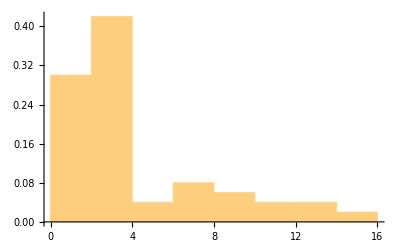

```mathematica
ph=Histogram[(√(#1.#1)&)/@Transpose[fin]⟦2⟧,Automatic(*{0,8,0.5}*),"Probability"]
```

We can calculate the temperature T of our gas from  its average kinetic energy per particle:
  1/2 m v^2 = 3/2 k_B T

```mathematica
temp=m Plus@@Map[#.#&,Transpose[fin][[2]]]/(3 Length[fin]1.38 10^-23)/.params
```

0.0235257

Some thermal physics, which you have met this term, tells us that we should expect a distribution of particle speeds which depends on the temperature, 
   p(c) = A c^2 ⅇ^(-m c^2/2 k_B T),
   where A is the normalisation constant
     √(2/π)(m/(T k_B))^(3/2)
   so for Neon we expect

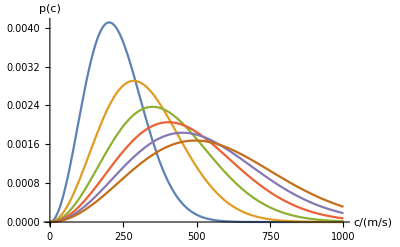

```mathematica
Plot[Evaluate[Table[√(2/π) (m/(T Subscript[k, B]))^(3/2) c^2 ⅇ^(-(m c^2)/(2 Subscript[k, B] T))/.params/.Subscript[k, B]->1.38/10^23,{T,50,300,50}]],{c,0,1000},PlotRange->All,AxesLabel->{"c/(m/s)","p(c)"}]
```

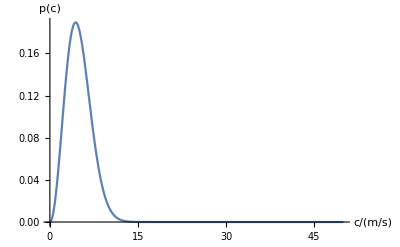

```mathematica
Plot[Evaluate[√(2/π) (m/(T Subscript[k, B]))^(3/2) c^2 ⅇ^(-(m c^2)/(2 Subscript[k, B] T))/.params/.Subscript[k, B]->1.38/10^23/.T->temp],{c,0,50},PlotRange->All,AxesLabel->{"c/(m/s)","p(c)"}]
```

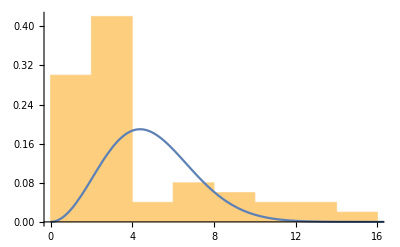

```mathematica
Show[ph,%]
```

This shows us that molecular dynamics needs quite long runs in order to produce sensible results, especially if we start the particles from rest as we did here. In general, one must divide calculations into two stages:
          a) Equilibration: this allows the system to 'settle down'. In our example, we started with no kinetic energy, so we have to allow the particles to move around enough, interacting through the potential, to achieve the right balance between kinetic and potential energy (in fact there is a powerful theorem, the virial theorem, which says that for particles interacting through an inverse square law force the total kinetic energy T and the total potential energy V are related by 2T+V=0, and this can be a useful check for electrostatic and gravitational systems).
          b) After a), one collects statistics on the behaviour of the particles, to evaluate the properties of interest.

We can do much better if we start off with appropriate kinetic energy, even if we just sample from a uniform distribution.  The code below just samples from a velocity distribution in which each particle has a component of  velocity in each direction between -2.8 and 2.8 times the average velocity. In practice, we would initialise from the correct distribution.

```mathematica
initpert[n_,L_,T_]:=For[en=10^10;tries=0;vav=√((2.8 1.38 T)/(10^23 m))/.params,(Abs[en]>ϵ/.params)&&tries<100,tries++,dat=Table[{L RandomReal[{0,1},3],RandomReal[{-vav,vav},3]},{i,1,n}]/.params;
en=etot[Transpose[dat][[1]],L]]
```

```mathematica
blen=3 10^-8;
initpert[500,blen,100]
tries
en
```

1

-1.11075×10^-22

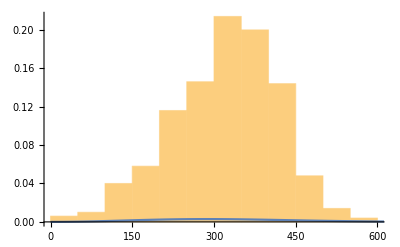

```mathematica
ph=Histogram[(√(#1.#1)&)/@Transpose[dat]⟦2⟧,(*{0,600,30}*)Automatic,"Probability"];
pa=Plot[Evaluate[√(2/π) (m/(T Subscript[k, B]))^(3/2) c^2 ⅇ^(-(m c^2)/(2 Subscript[k, B] T))/.params/.Subscript[k, B]->1.38/10^23/.T->100],{c,0,1000},PlotRange->All,AxesLabel->{"c/(m/s)","p(c)"}];
Show[ph,pa]
```

What we have done here is not a realistic example of how molecular dynamics would be used. If we were trying to model a gas, we would need a much larger volume and longer simulation (because the mean free path of a molecule, that is, the distance it travels before it has a collision, is typically about 1000 times the molecular size at room temperature). On the other hand, if we were trying to model a condensed phase (liquid or solid) we would start from a structure with more local order and with the molecules packed more closely together. The plan was to introduce the ideas.

It is worth noting that the molecular dynamics scheme we have developed here is based on smooth, continuous interaction potentials. There is another version, suitable for modelling hard spheres bouncing off one another, which is called 'event-driven' molecular dynamics. In that scheme molecules only interact when they collide. The scheme, then, is to let the molecules travel at constant velocity in straight lines, calculate the time until the next 'event', when two of them collide (or one collides with the walls of the container). Then move the molecules the distance appropriate to that time interval, alter the velocities of the molecules involved in the 'event', and continue. This is the subject of one of the mini-projects for this course.

## Large and small

Simulations with large numbers of particles are used in simulating plasmas (for example, in nuclear fusion experiments), where the particles are atoms and electrons, and in modelling galaxies, where the particles are stars (actually, these models also need to account for a continuous distribution of matter in the form of dust). In both these cases the interaction force between particles follows an inverse square law (electrostatic or gravitational), and there are more efficient ways of calculating the forces than by summing every pairwise interaction. These methods rely on the fact that the gravitational and electrostatic fields obey Poisson's equation
  ∇^2 ϕ = ϱ
  (give or take a constant or two), and there are fast techniques for solving that equation based on Fast Fourier Transform methods (which are beyond the scope of this course).
  
Another method for speeding up molecular dynamics simulations is the 'neighbour list' scheme. This keeps a record, for each particle, of which other particles are close enough for their interactions to matter: if each of the N particles has, on average, n particles within its sphere of influence then the number of interactions to be counted is nN/2 rather than N^2/2, which can be a significant saving for a large simulation. Of course, this neighbour list changes as the molecules move about, so from time to time one has to look at all the interactions and update the neighbour lists, but this need not be done every time-step.

## Simple gravitational systems

Although simulations on large numbers of particles are hard to do efficiently in Mathematica, we can model some systems with small numbers of particles and see interesting results. Examples include the presence of so-called 'Lagrange points' -- 

We could use the same integration methods here as for molecular dynamics. The only difference is in the potential  which is gravitational rather than of the Lennard-Jones form. We also have to handle particles which have different masses. For a bit of variety, and as we are only going to look at a small number of 'particles', we shall set up the equations specifically and let Mathematica integrate them using NDSolve.  
  
First, consider the Earth-Moon system. The equations of motion are

```mathematica
G=6.673 10^-11;me=5.98 10^24;mm=9.35 10^22;
re[t_]={xe[t],ye[t],ze[t]};
rm[t_]={xm[t],ym[t],zm[t]};
eqe=me D[re[t], t,t] ==-mm me G(re[t]-rm[t])/((re[t]-rm[t]).(re[t]-rm[t]))^(3/2);
eqm=mm D[rm[t], t,t] ==mm  me G(re[t]-rm[t])/((re[t]-rm[t]).(re[t]-rm[t]))^(3/2);
```

#### Explanation

Define the physical parameters

```mathematica
G=6.673 10^-11;me=5.98 10^24;mm=9.35 10^22;
```

and, for later convenience, define the position vectors of the earth and the moon in terms of their components.

```mathematica
re[t_]={xe[t],ye[t],ze[t]};
rm[t_]={xm[t],ym[t],zm[t]};
```

Note that for a general-purpose problem with an arbitrary number of particles we could define vectors r[n][t], n representing an index number for the particle.

Then the equations of motion can be written in terms of the vectors -- noting that the force of the earth on the moon is equal and opposite to the force of the moon on the earth.

```mathematica
eqe=me D[re[t], t,t] ==-mm me G(re[t]-rm[t])/((re[t]-rm[t]).(re[t]-rm[t]))^(3/2);
eqm=mm D[rm[t], t,t] ==mm  me G(re[t]-rm[t])/((re[t]-rm[t]).(re[t]-rm[t]))^(3/2);
```

Now initialise. We know the orbital period of the Moon is about 28 days, so if we start with the centre of gravity of the Earth-Moon system at the origin we have

```mathematica
Rem=3.84 10^8;period=28*24*60*60;
re0={-mm Rem/(me+mm),0,0};
rm0={me Rem/(me+mm),0,0};
ve0={0,2 π re0[[1]]/period,0};
vm0={0,2 π rm0[[1]]/period,0};
```

Now we can set up the equations. As we need a list of equations, not a list of equations which themselves involve lists, we need to use Thread. As we see from what follows, the effect of Thread is to convert {ax, ay, az}=={fx[r], fy[r], fz[r]} to {ax==fx[r], ay==fy[r], az=fz[r]}.

```mathematica
eqe
Thread[eqe]
```

{5.98×10^24 xe''[t],5.98×10^24 ye''[t],5.98×10^24 ze''[t]}=={-(3.73107×10^37 (xe[t]-xm[t]))/(((xe[t]-xm[t])^2+(ye[t]-ym[t])^2+(ze[t]-zm[t])^2)^(3/2)),-(3.73107×10^37 (ye[t]-ym[t]))/(((xe[t]-xm[t])^2+(ye[t]-ym[t])^2+(ze[t]-zm[t])^2)^(3/2)),-(3.73107×10^37 (ze[t]-zm[t]))/(((xe[t]-xm[t])^2+(ye[t]-ym[t])^2+(ze[t]-zm[t])^2)^(3/2))}

{5.98×10^24 xe''[t]==-(3.73107×10^37 (xe[t]-xm[t]))/(((xe[t]-xm[t])^2+(ye[t]-ym[t])^2+(ze[t]-zm[t])^2)^(3/2)),5.98×10^24 ye''[t]==-(3.73107×10^37 (ye[t]-ym[t]))/(((xe[t]-xm[t])^2+(ye[t]-ym[t])^2+(ze[t]-zm[t])^2)^(3/2)),5.98×10^24 ze''[t]==-(3.73107×10^37 (ze[t]-zm[t]))/(((xe[t]-xm[t])^2+(ye[t]-ym[t])^2+(ze[t]-zm[t])^2)^(3/2))}

Set up and solve the equations using Mathematica's built-in function. Note that we Join the differential equations to the boundary conditions.

```mathematica
tmax=period ;
orbits=Join[re[t],rm[t]]/.NDSolve[Join[Thread[eqe],Thread[eqm],Thread[re[0]==re0],Thread[rm[0]==rm0],Thread[((D[re[t], t])/.t->0)==ve0],Thread[((D[rm[t], t])/.t->0)==vm0]],Join[re[t],rm[t]],{t,0,tmax}][[1]]
```

{                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t]}

```mathematica
ParametricPlot3D[Take[orbits,-3],{t,0,tmax},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Now let's add a geostationary satellite to the mix. Will the behaviour depend on the plane of the Earth-satellite system relative to the Earth-Moon system? As the satellite is so light, we can neglect any changes to the overall centre of mass of the system. Similarly, we can neglect any perturbation of the orbits of the Earth and the Moon by the satellite.

This just adds one more vector differential equation.

```mathematica
ms=1000;
rs[t_]={xs[t],ys[t],zs[t]};
eqs=ms D[rs[t], t,t] ==ms  me G(re[t]-rs[t])/((re[t]-rs[t]).(re[t]-rs[t]))^(3/2)+ms  mm G(rm[t]-rs[t])/((rm[t]-rs[t]).(rm[t]-rs[t]))^(3/2);
```

Start with the satellite in the Earth-Moon plane. We happen to know (especially if we attended all the first year Mechanics problems classes!) the radius of a geostationary orbit.

```mathematica
Res=4.225 10^7;periods=24*60*60;
rs0=re0-{Res,0,0};
vs0=ve0+{0,2 π Res/periods,0};
```

This time, plot the orbit of the satellite

```mathematica
tmax=period;
orbits=Join[re[t],rm[t],rs[t]]/.NDSolve[Join[Thread[eqe],Thread[eqm],Thread[eqs],Thread[re[0]==re0],Thread[rm[0]==rm0],Thread[rs[0]==rs0],Thread[(D[re[t], t]/.t->0)==ve0],Thread[(D[rm[t], t]/.t->0)==vm0],Thread[(D[rs[t], t]/.t->0)==vs0]],Join[re[t],rm[t],rs[t]],{t,0,tmax}]⟦1⟧
ParametricPlot3D[Take[orbits,-3],{t,0,tmax},AxesLabel->{"x","y","z"}]
```

{                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t]}

-Graphics3D-

The above plot looks disastrous -- but it's only the plotting that is letting us down, and trying again with more points in the plot (note that we are using the same InterpolatingFunction as before, just sampling it more frequently) improves the picture.

Of course, what is really of interest, from our geocentric viewpoint, is the motion of the satellite relative to the Earth:

```mathematica
p1=ParametricPlot3D[Take[orbits,-3]-Take[orbits,3],{t,0,tmax},PlotPoints->1000,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

Now try having the satellite in the perpendicular plane. All we need to alter is the initial conditions for the satellite.

```mathematica
Res=4.225 10^7;periods=24*60*60;
rs0=re0-{0,Res,0};
vs0=ve0+{0,0,2 π Res/periods};
```

The solving and plotting is as before.

```mathematica
tmax=period;
orbits=Join[re[t],rm[t],rs[t]]/.NDSolve[Join[Thread[eqe],Thread[eqm],Thread[eqs],Thread[re[0]==re0],Thread[rm[0]==rm0],Thread[rs[0]==rs0],Thread[(D[re[t], t]/.t->0)==ve0],Thread[(D[rm[t], t]/.t->0)==vm0],Thread[(D[rs[t], t]/.t->0)==vs0]],Join[re[t],rm[t],rs[t]],{t,0,tmax}]⟦1⟧
ParametricPlot3D[Take[orbits,-3]-Take[orbits,3],{t,0,tmax},PlotPoints->1000,AxesLabel->{"x","y","z"}]
```

{                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t],                                     6
InterpolatingFunction[{{0., 2.4192 10 }}, <>][t]}

-Graphics3D-

We can conclude, then, that the Moon's gravitation has negligible influence on the orbit of a geostationary satellite.

The ability to calculate orbits and trajectories is, of course, essential in the planning of spacecraft missions. Many of these missions depend on so-called 'slingshot' orbits, where a craft loops around one of the planets to gain kinetic energy.

## Particles as 'lumps of matter'

We can also use particle models in a more abstract sense. If we imagine 'lumps of material', held together by some force, for example

```mathematica
cnst=10^4;
v[r_]:=cnst((1/r)^4 - (1/r)^2);
```

Find the equilibrium separation of the particles by finding where the gradient of the potential is zero.

```mathematica
D[v[r],r]
```

10000 (-4/r^5+2/r^3)

```mathematica
Solve[D[v[r],r]==0,r]
```

{{r→-√2},{r→√2}}

Define a function to produce the force between two particles at a vector separation rrel:

```mathematica
acc[rrel_List]:=-cnst(2/(rrel.rrel)^2-4/(rrel.rrel)^3)rrel
```

then we can set up a chain of lumps of material, representing the chain of a suspension bridge, for example. We define a function to set up a chain of n particles, with zero velocity, separated by the equilibrium separation, and plot the result using the function we defined before.

```mathematica
initbc[n_]:=dat=Table[{2^(1/2){i,n /2,n /2},{0.,0.,0.}},{i,0,n}];
initbc[20];
blen=dat[[-1,1,1]]-dat[[1,1,1]];
ppper[dat,blen]
```

-Graphics3D-

Now let's turn on gravity, and see how the chain behaves.

```mathematica
bc1=dat[[1]];
bc2=dat[[-1]];
accv[dat_]:=Map[acc,dat-RotateRight[dat],1]+Map[acc,dat-RotateLeft[dat],1]+Table[{0,0,-10},{i,1,Length[dat]}]
updvVbc[d_,Δt_]:=Module[{a,an,x,xn,v},
{x,v}=Transpose[d];
a=accv[x];
xn=x +Δt v+Δt^2 a/2;
xn[[1]]=bc1[[1]];
xn[[-1]]=bc2[[1]];
an=accv[xn];
v=v+Δt(a+an)/2 ;
v[[1]]=bc1[[2]];
v[[-1]]=bc2[[2]];
Transpose[{xn,v }]]
```

#### Explanation:

First, save the positions and velocities of the particles at each end of the chain.

```mathematica
bc1=dat[[1]];
bc2=dat[[-1]];
```

Next, define the acceleration function:

```mathematica
accv[dat_]:=-Map[acc,dat-RotateRight[dat],1]-Map[acc,dat-RotateLeft[dat],1]-Table[{0,0,9.8},{i,1,Length[dat]}]
```

Map[acc,dat-RotateRight[dat],1] takes the separation of an atom from the atom to its left, and calculates this force, acc then adds the force from the atoms to the right, and then adds the constant acceleration due to gravity.

```mathematica
updvVbc[d_,Δt_]:=Module[{a,an,x,xn,v},
{x,v}=Transpose[d];
a=accv[x];
xn=x +Δt v+Δt^2 a/2;
xn[[1]]=bc1[[1]];
xn[[-1]]=bc2[[1]];
an=accv[xn];
v=v+Δt(a+an)/2 ;
```

So far the update function is as before. Next we apply the boundary conditions to fix the end particles,

```mathematica
v[[1]]=bc1[[2]];
v[[-1]]=bc2[[2]];
```

and construct the updated positions and velocities.

```mathematica
Transpose[{xn,v }]]
```

Now run the calculation for 2000 steps of 1/1000 seconds, but do this in blocks of 100 steps, plotting the result after every 100.

```mathematica
fin=dat;
ListAnimate[Table[fin=Nest[updvVbc[#1,10^-3]&,fin,100];Print[i];ppper[fin,blen],{i,1,20}]]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

We see the chain falling into the characteristic shape of a catenary, and then oscillating about the equilibrium position. If we built a damping mechanism into the update scheme (for example, by reducing all the velocities by a constant factor at each step), we would see the chain settle down.  This is done in one of the exercises.

## Summary

This lecture has only scraped the surface of the sort of modelling that can be done based on particles. The book Particle Modelling by Donald Greenspan (Birkhauser, 1997) gives a range of applications, ranging from fluid flow to biological self-organisation. Here is an example -- a model of the formation and detachment of a liquid drop. The simulation involved 1454 mobile particles, with an additional 201 fixed particles to represent the flat plate. Slightly different force laws were used for fluid-fluid and fluid-solid interactions, and the simulation was run for 5000 time steps.

-Graphics-

A.H. Harker
Physics and Astronomy, UCL
February 2008, revised February 2009, February 2010.
Amended by Patrick Guio, Physics and Astronomy, UCL, spring 2015, 2016 and 2017.